```mathematica
Ωm=0.306;
Ωr=9.03 10^-5;
ΩΛ=0.692;
H0=(1.4432 10^10)^-1;
```

```mathematica
dt[a_]:=1/(H0 √(Ωm a^-1+Ωr a^-2+ΩΛ a^2))
```

```mathematica
time[a_]:=NIntegrate[dt[A],{A,0,a}]
```

```mathematica
time[1]
```

1.38371×10^10

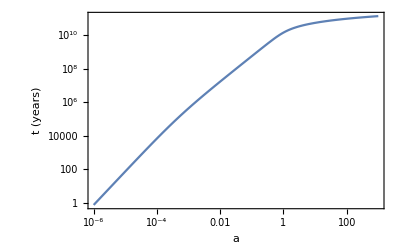

```mathematica
LogLogPlot[time[a],{a,10^-6,10^3},Frame->True,FrameLabel->{"a","t (years)"}]
```

```mathematica
Create a log-spaced list of scale factor/times
```

```mathematica
times= Table[{10^a,time[10^a]},{a,-6,3,0.01}];
```

```mathematica
Reverse the ordering of the list to create times/scale factors
```

```mathematica
reversedtimes=Map[{#[[2]],#[[1]]}&,times];
```

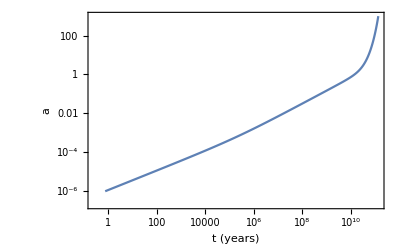

```mathematica
ListLogLogPlot[reversedtimes,Frame->True,Joined->True,FrameLabel->{"t (years)","a"}]
```

```mathematica
interpolateda:=Interpolation[reversedtimes]
```

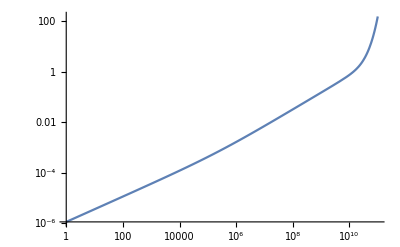

```mathematica
LogLogPlot[interpolateda[t],{t,1,10^11}]
```

```mathematica
Hubble[t]:=(D[interpolateda[x],x]/.{x->t})/interpolateda[t]
```

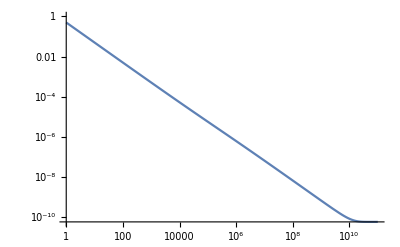

```mathematica
LogLogPlot[Hubble[t],{t,1,10^11}]
```